```mathematica
ClearAll["Global`*"];
```

```mathematica
dataStandingVariation=Import[NotebookDirectory[]<>"../Data/"<>"Table_standing_variants_seedbank_strength_1herb_10no.txt","CSV"];
dataWaitingTimeSeedBankStrength=Import[NotebookDirectory[]<>"../Data/"<>"Table_MGWP_WaitingTime_SeedBankStrength.txt","CSV"];
```

## Waiting times till rescue under different seed bank strength

### Parameters constant under different seed bank strength

#### Parameters of the model

```mathematica
b=0.9 140;
dZ=0.35;
gZ = 0.2;
f=0.9 13000;
dS=0.94;
c=0.3;
kc=0.5;
cr = {0,kc c,c};
```

```mathematica
T=b(1-dZ)gZ;
S = (1-cr)f(1-dS);
```

```mathematica
p=0.95;
μ=10^-8;
hl=0.998;
ht=0.985;
kh=0.5;
hL = {hl,(1-kh) hl, 0};
hT = {ht,(1-kh) ht, 0};
```

```mathematica
A=10^2;
```

```mathematica
M={(1-μ)^2 {{1,0.5,0},{0.5,0.25,0},{0,0,0}}+μ(1-μ) {{0,0.5,1},{0.5,0.5,0.5},{1,0.5,0}}+μ^2{{0,0,0},{0,0.25,0.5},{0,0.5,1}},2 μ (1-μ) {{1,0.5,0},{0.5,0.25,0},{0,0,0}}+((1-μ)^2 +μ^2) {{0,0.5,1},{0.5,0.5,0.5},{1,0.5,0}}+2 μ (1-μ){{0,0,0},{0,0.25,0.5},{0,0.5,1}},μ^2 {{1,0.5,0},{0.5,0.25,0},{0,0,0}}+μ {{0,0.5,1},{0.5,0.5,0.5},{1,0.5,0}}+{{0,0,0},{0,0.25,0.5},{0,0.5,1}}}//N;
```

### Waiting time distribution for germination probability g = 0.2 and adapted seed bank death

```mathematica
nMax=30;
```

#### Germination probability and adapted seed bank death

```mathematica
g=0.2;
dB=0.48 g /(1-g)(1-0.3)/0.3;
```

#### Parameters of the offspring distributions

```mathematica
λ[i_,j_]:=(M[[j,i,i]] p S[[i]]+M[[j,i,1]] (1-p)(S[[i]]+(1-KroneckerDelta[1,i]) S[[1]]))g (1-hL[[j]])+KroneckerDelta[j,i]T(1-hT[[j]]);
λm[i_,j_]:=(M[[j,i,i]] p S[[i]]+M[[j,i,1]] (1-p)(S[[i]]+(1-KroneckerDelta[1,i]) S[[1]]))(1-g);
```

```mathematica
α=(1-dB) g (1-hL);
β=(1-dB) (1-g);
γ=(dB+(1-dB) g hL);
```

#### Offspring generating function

```mathematica
G[s_]:={Exp[λ[1,1] (s[[1]]-1)+ λ[1,2] (s[[2]]-1)+ λ[1,3] (s[[3]]-1)+ λm[1,1] (s[[4]]-1)+ λm[1,2] (s[[5]]-1)+ λm[1,3] (s[[6]]-1)],0,0,α[[1]]s[[1]]+β s[[4]]+γ[[1]],α[[2]]s[[2]]+β s[[5]]+γ[[2]],α[[3]]s[[3]]+β s[[6]] +γ[[3]]}
```

#### Standing genetic variation

```mathematica
pos=Position[dataStandingVariation⟦All,{1}⟧,{g}]⟦1,1⟧;
v = {dataStandingVariation[[pos]][[6]],dataStandingVariation[[pos]][[7]],dataStandingVariation[[pos]][[8]],dataStandingVariation[[pos]][[3]],dataStandingVariation[[pos]][[4]],dataStandingVariation[[pos]][[5]]};
```

#### Waiting time till the first resistant plant establishes on the field

```mathematica
Π[n_]:=Nest[G[#]&,{1,0,0,1,1,1},n];
```

```mathematica
F[n_]:=1-Exp[A( v[[1]] (Π[n][[1]]-1)+v[[4]] (Π[n][[4]]-1)+v[[5]] (Π[n][[5]]-1)+v[[6]] (Π[n][[6]]-1))]
```

```mathematica
P1=Prepend[Table[F[n]-F[n-1],{n,1,nMax}],1-Exp[-A(v[[2]]+v[[3]])]];
P1b=Prepend[Table[F[n],{n,1,nMax}],1-Exp[-A(v[[2]]+v[[3]])]];
```

```mathematica
g20=Partition[Riffle[Table[n,{n,0,nMax}],P1],2];
```

```mathematica
g20b=Partition[Riffle[Table[n,{n,0,nMax}],P1b],2];
```

#### Waiting time estimates from simulations

```mathematica
pos20=Flatten[Position[dataWaitingTimeSeedBankStrength⟦All,{1}⟧,{g}]];
```

```mathematica
dataWaitingTimeSeedBankStrength20=dataWaitingTimeSeedBankStrength⟦pos20,All⟧;
```

```mathematica
dataWaitingTimeSeedBankStrengthCumulative20=dataWaitingTimeSeedBankStrength20;
dataWaitingTimeSeedBankStrengthCumulative20[[All,3]]=Accumulate[dataWaitingTimeSeedBankStrengthCumulative20[[All,3]]];
```

### Waiting time distribution for germination probability g = 0.4 and adapted seed bank death

#### Germination probability and adapted seed bank death

```mathematica
g=0.4;
dB=0.48 g /(1-g)(1-0.3)/0.3;
```

#### Parameters of the offspring distributions

```mathematica
λ[i_,j_]:=(M[[j,i,i]] p S[[i]]+M[[j,i,1]] (1-p)(S[[i]]+(1-KroneckerDelta[1,i]) S[[1]]))g (1-hL[[j]])+KroneckerDelta[j,i]T(1-hT[[j]]);
λm[i_,j_]:=(M[[j,i,i]] p S[[i]]+M[[j,i,1]] (1-p)(S[[i]]+(1-KroneckerDelta[1,i]) S[[1]]))(1-g);
```

```mathematica
α=(1-dB) g (1-hL);
β=(1-dB) (1-g);
γ=(dB+(1-dB) g hL);
```

#### Offspring generating function

```mathematica
G[s_]:={Exp[λ[1,1] (s[[1]]-1)+ λ[1,2] (s[[2]]-1)+ λ[1,3] (s[[3]]-1)+ λm[1,1] (s[[4]]-1)+ λm[1,2] (s[[5]]-1)+ λm[1,3] (s[[6]]-1)],0,0,α[[1]]s[[1]]+β s[[4]]+γ[[1]],α[[2]]s[[2]]+β s[[5]]+γ[[2]],α[[3]]s[[3]]+β s[[6]] +γ[[3]]}
```

#### Standing genetic variation

```mathematica
pos=Position[dataStandingVariation⟦All,{1}⟧,{g}]⟦1,1⟧;
v = {dataStandingVariation[[pos]][[6]],dataStandingVariation[[pos]][[7]],dataStandingVariation[[pos]][[8]],dataStandingVariation[[pos]][[3]],dataStandingVariation[[pos]][[4]],dataStandingVariation[[pos]][[5]]};
```

#### Waiting time till the first resistant plant establishes on the field

```mathematica
Π[n_]:=Nest[G[#]&,{1,0,0,1,1,1},n];
```

```mathematica
F[n_]:=1-Exp[A( v[[1]] (Π[n][[1]]-1)+v[[4]] (Π[n][[4]]-1)+v[[5]] (Π[n][[5]]-1)+v[[6]] (Π[n][[6]]-1))]
```

```mathematica
P2=Prepend[Table[F[n]-F[n-1],{n,1,nMax}],1-Exp[-A(v[[2]]+v[[3]])]];
P2b=Prepend[Table[F[n],{n,1,nMax}],1-Exp[-A(v[[2]]+v[[3]])]];
```

```mathematica
g40=Partition[Riffle[Table[n,{n,0,nMax}],P2],2];
g40b=Partition[Riffle[Table[n,{n,0,nMax}],P2b],2];

gb=Partition[Riffle[Table[n,{n,0,nMax}],P1-P2],2];
```

#### Waiting time estimates from simulations

```mathematica
pos40=Flatten[Position[dataWaitingTimeSeedBankStrength⟦All,{1}⟧,{g}]];
```

```mathematica
dataWaitingTimeSeedBankStrength40=dataWaitingTimeSeedBankStrength⟦pos40,All⟧;
```

```mathematica
dataWaitingTimeSeedBankStrengthCumulative40=dataWaitingTimeSeedBankStrength40;
dataWaitingTimeSeedBankStrengthCumulative40[[All,3]]=Accumulate[dataWaitingTimeSeedBankStrengthCumulative40[[All,3]]];
```

### Comparison of waiting time distributions for different seed bank strength

#### Cumulative waiting time distribution

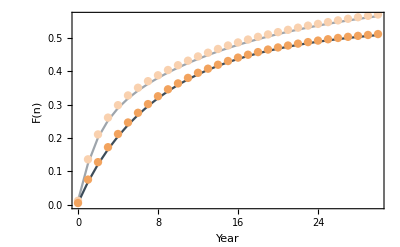

```mathematica
Show[ListPlot[{g20b,g40b},PlotRange->Full,Joined->True,PlotStyle->{Directive[Lighter[RGBColor["#3C4C59"],0.5]],Directive[Lighter[RGBColor["#3C4C59"],0]]}],ListPlot[dataWaitingTimeSeedBankStrengthCumulative20⟦1;;nMax+1,{2,3}⟧,PlotStyle->Directive[Lighter[RGBColor["#F2A35E"],0.5],PointSize[0.015],Opacity[1]]],ListPlot[dataWaitingTimeSeedBankStrengthCumulative40⟦1;;nMax+1,{2,3}⟧,PlotStyle->Directive[RGBColor["#F2A35E"],PointSize[0.015],Opacity[1]],PlotRange->{{-1,nMax+1},{-.0015,0.65}}],Frame->True,FrameStyle->Directive[Black,Thickness[0.003]],FrameLabel->{"Year","F(n)"}]
```

#### Probability density function of waiting time

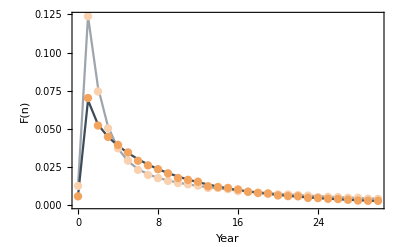

```mathematica
Show[ListPlot[{g20,g40},PlotRange->Full,Joined->True,PlotStyle->{Directive[Lighter[RGBColor["#3C4C59"],0.5]],Directive[Lighter[RGBColor["#3C4C59"],0]]}],ListPlot[dataWaitingTimeSeedBankStrength20⟦1;;nMax+1,{2,3}⟧,PlotStyle->Directive[Lighter[RGBColor["#F2A35E"],0.5],PointSize[0.015],Opacity[1]]],ListPlot[dataWaitingTimeSeedBankStrength40⟦1;;nMax+1,{2,3}⟧,PlotStyle->Directive[RGBColor["#F2A35E"],PointSize[0.015],Opacity[1]],PlotRange->{{-1,nMax+1},{-.0015,0.15}}],Frame->True,FrameStyle->Directive[Black,Thickness[0.003]],FrameLabel->{"Year","F(n)"}]
```